```mathematica
F[x_]:=If[x≤-2,Return[-2x+3],
If[-2<x<5,Return[5],Return[x^2-3x]
];];
```

```mathematica
F[-10]
```

23

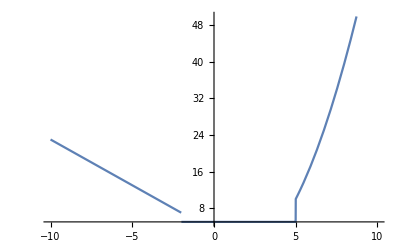

```mathematica
Plot[F[x],{x,-10,10}]
```

```mathematica
Solve[F[x]==2,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[If[x≤-2,Return[-2 x+3],If[-2<x<5,Return[5],Return[x^2-3 x]];]==2,x]